-1.

0.980198

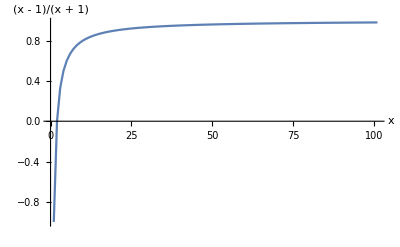

```mathematica
data=Table[N[((i-1)/(i+1))],{i,0,100}];
Min[data]
Max[data]
plot=ListPlot[data,PlotRange->All, Joined->True,AxesLabel->{Style["x",10],Style["(x - 1)/(x + 1)",10]}, ImagePadding->{{30,30},{10,50}}]
```

```mathematica
Export["Approximation_F.jpeg", plot]
```

Approximation_F.jpeg

```mathematica
Plo
```